```mathematica
ClearAll["Global`*"]
```

# Separatrix plot - Phase diagram

```mathematica
f1[u_]:=1;
f2[u_]:=0;
f3[u_,v_]:=Sqrt[v];
f4[u_,v_]:=v;
f5[u_,v_]:=-v;
```

```mathematica
export[object_,name_]:=Export[StringTemplate["/Users/basavyr/Offline-Work/Repos/phdthesis/Chapters/Figures/``.pdf"][name],object,ImageResolution->1500];
```

```mathematica
inseter[text_,pos_,color_]:=Inset[Style[StringTemplate["``"][text],color,Bold,21,FontFamily->"Latin Modern Roman"],Scaled[{pos[[1]],pos[[2]]}]];
```

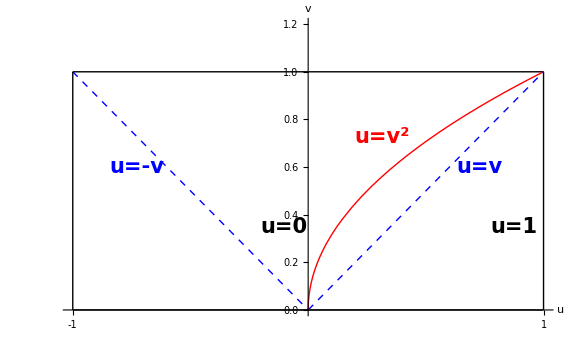

```mathematica
phaseD=Plot[{f1[u],f2[u],f3[u,u],f4[u,u],f5[u,u]},{u,-1,1},
PlotRange->{0,1.2},
AspectRatio->Automatic,
Frame->False,Axes->True,
Ticks->{{-1,1},None},
LabelStyle->{21,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->{{Black,Thick},
{Black,Thick},
{Red,Thick},
{Blue,Thick,Dashed},
{Blue,Thick,Dashed}
},
AxesStyle->Directive[Thick,Black],
AxesLabel->{"u","v"},
ImageSize->Large,
Epilog->{inseter["u=-v",{0.15,0.5},Blue],
inseter["u=v",{0.85,0.5},Blue],
inseter["u=v^2",{0.65,0.6},Red],
inseter["u=0",{0.45,0.3},Black],
inseter["u=1",{0.92,0.3},Black]
}
];
Show[phaseD,Graphics[{Thick,Black,Line[{{1,0},{1,1}}]}],Graphics[{Thick,Black,Line[{{-1,0},{-1,1}}]}]]
export[Show[phaseD,Graphics[{Thick,Black,Line[{{1,0},{1,1}}]}],Graphics[{Thick,Black,Line[{{-1,0},{-1,1}}]}]],"new-boson-separatrix-diagram"];
```